# Electrostatic potential and reorganization energy for arbitrary charge distributions near metal electrode covered with dielectric

## Spherical and cylindrical cavities

```mathematica
<<VectorAnalysis`
```

## Units

```mathematica
bohr2a=0.529177`10;
a2bohr=1/bohr2a;
au2kcal=627.5095`10;
kcal2au=1/au2kcal;
ev2cm=8065.54477`10;
cm2ev = 1/ev2cm ;
au2ev=27.2113`10;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
```

## Parameters

Dielectric permittivities:
solvent: ϵ_s
SAM: ϵ_m

Geometry:
R - Radius of a shperical cavity around the charge
d - distance from the charge to the electrode surface.

```mathematica
ϵs=35.688;
ϵsinf=1.8;
```

```mathematica
ϵm=2.25;
ϵminf=2.25;
```

## Model

### Spherical cavity

```mathematica
Graphics3D[{
{Opacity[0.5],Sphere[{0,0,0},0.75]},
{LightBlue,Opacity[0.5],Cuboid[{-1,-1,1.0},{1,1,1.5}]},
{Pink,Opacity[0.5],Cuboid[{-1,-1,1.5},{1,1,2.5}]},
{Opacity[0.0],Cuboid[{-1,-1,-1},{1,1,1.5}]},
{Text["I (ϵ_s)",{-0.9,1,-0.9},{-1,0}]},
{Text["II (ϵ_m)",{-0.9,1,1.1},{-1,0}]},
{Text["III (ϵ=∞)",{-0.9,1,1.6},{-1,0}]},
{Arrowheads[0.02],Arrow[{{-1.5,0,0},{1.5,0,0}}]},
{Text["x",{1.55,0,-0.05}]},
{Arrowheads[0.02],Arrow[{{0,-1.5,0},{0,1.5,0}}]},
{Text["y",{0,1.55,0.05}]},
{Arrowheads[0.02],Arrow[{{0,0,-1.5},{0,0,3.0}}]},
{Text["z",{-0.05,0.25,3.0}]},
{Text["0",{-0.05,0.05,-0.05}]},
{PointSize[Tiny],Point[Table[{0,0.75Cos[(2π(i-1))/200],0.75Sin[(2π(i-1))/200]},{i,1,201}]]},
{PointSize[Tiny],Point[Table[{0.75Cos[(2π(i-1))/200],0,0.75Sin[(2π(i-1))/200]},{i,1,201}]]},
{PointSize[Tiny],Point[Table[{0.75Cos[(2π(i-1))/200],0.75Sin[(2π(i-1))/200],0},{i,1,201}]]},
{Point[{0,0,0.75}]},
{Point[{0,0.75,0}]},
{Point[{0.75,0,0}]},
{Point[{0,0,-0.75}]},
{Point[{0,-0.75,0}]},
{Point[{-0.75,0,0}]},
{Point[{0,0,1}]},
{Point[{0,0,1.5}]},
{Text["R",{-0.05,0.1,0.80}]},
{Text["d",{-0.05,0.1,1.0}]},
{Text["d+δ",{-0.05,0.1,1.5}]}
},Boxed->False,ImageSize->Large,ViewPoint->{2,10,-1}]
```

-Graphics3D-

### Cylindrical Cavity

```mathematica
Graphics3D[{
{Opacity[0.5],Cylinder[{{0,0,-0.75},{0,0,0.75}},0.75]},
{LightBlue,Opacity[0.5],Cuboid[{-1,-1,1.0},{1,1,1.5}]},
{Pink,Opacity[0.5],Cuboid[{-1,-1,1.5},{1,1,2.5}]},
{Opacity[0.0],Cuboid[{-1,-1,-1},{1,1,1.5}]},
{Text["I (ϵ_s)",{-0.9,1,-0.9},{-1,0}]},
{Text["II (ϵ_m)",{-0.9,1,1.1},{-1,0}]},
{Text["III (ϵ=∞)",{-0.9,1,1.6},{-1,0}]},
{Arrowheads[0.02],Arrow[{{-1.5,0,0},{1.5,0,0}}]},
{Text["x",{1.55,0,-0.05}]},
{Arrowheads[0.02],Arrow[{{0,-1.5,0},{0,1.5,0}}]},
{Text["y",{0,1.55,0.05}]},
{Arrowheads[0.02],Arrow[{{0,0,-1.5},{0,0,3.0}}]},
{Text["z",{-0.05,0.25,3.0}]},
{Text["0",{-0.05,0.05,-0.05}]},
{PointSize[Tiny],Point[Table[{0.75Cos[(2π(i-1))/200],0.75Sin[(2π(i-1))/200],0},{i,1,201}]]},
{Point[{0,0,0.75}]},
{Point[{0,0.75,0}]},
{Point[{0.75,0,0}]},
{Point[{0,0,-0.75}]},
{Point[{0,-0.75,0}]},
{Point[{-0.75,0,0}]},
{Point[{0,0,1}]},
{Point[{0,0,1.5}]},
{Text["L/2",{-0.05,0.1,0.80}]},
{Text["d",{-0.05,0.1,1.0}]},
{Text["d+δ",{-0.05,0.1,1.5}]}
},Boxed->False,ImageSize->Large,ViewPoint->{2,10,-1}]
```

-Graphics3D-

## Coordinate transformations

```mathematica
CylindricalToSpherical[cyl_]:=Module[{ρ,x,y,z,r,θ,ϕ},
ρ=cyl⟦1⟧;
ϕ=cyl⟦2⟧;
z=cyl⟦3⟧;
r=√(ρ^2+z^2);
θ=ArcCos[z/(√(z^2+ρ^2))];
{r,θ,ϕ}
];
```

```mathematica
SphericalToCylindrical[sph_]:=Module[{r,θ,ϕ,ρ,z},
r=sph⟦1⟧;
θ=sph⟦2⟧;
ϕ=sph⟦3⟧;
ρ=r Sin[θ];
z=r Cos[θ];
{ρ,ϕ,z}
];
```

```mathematica
CoordinatesToCartesian[{r,θ,ϕ},Spherical]
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

```mathematica
CoordinatesToCartesian[{ρ,ϕ,z},Cylindrical]
```

{ρ Cos[ϕ],ρ Sin[ϕ],z}

```mathematica
CoordinatesFromCartesian[{x,y,z},Cylindrical]
```

{√(x^2+y^2),ArcTan[x,y],z}

```mathematica
CylindricalToSpherical[{ρ,ϕ,z}]
```

{√(z^2+ρ^2),ArcCos[z/(√(z^2+ρ^2))],ϕ}

```mathematica
SphericalToCylindrical[{r,θ,ϕ}]
```

{r Sin[θ],ϕ,r Cos[θ]}

## Polarization induced potentials (region I)

ρ is a nested list of the following structure:
Table[ { q_i, {x_i,y_i,z_i} }, {i, 1, N} ]

### Potential from the charge distribution ρ itself

```mathematica
Φ1[ϵ_,ρ_,{r_,ϕ_,z_}]:=Module[
{κ,nCharges,pot,Q,xyzi,xyz,dist},
nCharges=Length[ρ];
pot=0;
Do[
Q=ρ⟦i,1⟧;
xyzi=ρ⟦i,2⟧;
xyz=CoordinatesToCartesian[{r,ϕ,z},Cylindrical];
dist=Norm[xyz-xyzi]a2bohr;
pot+=Q/dist,
{i,1,nCharges}];
pot/ϵ
];
```

### Potentials from the image charges (polarization potentials)

```mathematica
Clear[Φ23]
```

```mathematica
Φ23[d_,δ_,ϵs_,ϵm_,ρ_,cylcoord_,OptionsPattern[{NS->100}]]:=Module[
{NN,κ,nCharges,pot,Q,xyz,xyzi,di,cylcoordi,ri,ϕi,zi,Φ2,Φ3},
NN=OptionValue[NS];
κ=(ϵm-ϵs)/(ϵm+ϵs);
nCharges=Length[ρ];
pot=0;
Do[
Q=ρ⟦i,1⟧;
xyzi=ρ⟦i,2⟧;
xyz=CoordinatesToCartesian[cylcoord,Cylindrical];
di=d-xyzi⟦3⟧;
cylcoordi=CoordinatesFromCartesian[xyz-xyzi,Cylindrical];
ri=cylcoordi⟦1⟧;
ϕi=cylcoordi⟦2⟧;
zi=cylcoordi⟦3⟧;
Φ2=If[κ==0,-Q 1/(a2bohr √(ri^2+(2di-zi)^2)),-Q Sum[(-κ)^n/(a2bohr √(ri^2+(2n δ+2di-zi)^2)),{n,0,NN}]];
Φ3=If[κ==0,-Q 1/(a2bohr √(ri^2+(2 δ+2di-zi)^2)),-Q Sum[(-κ)^n/(a2bohr √(ri^2+((2n+2) δ+2di-zi)^2)),{n,0,NN}]];
pot+=κ/ϵs Φ2+1/ϵs Φ3
,{i,1,nCharges,1}];
pot
];
```

```mathematica
Φ23[5.0,1.0,ϵs,ϵm,{{1,{0,0,0}}},{5.0,π/2,π/3},NS->100]
```

-0.0000712961

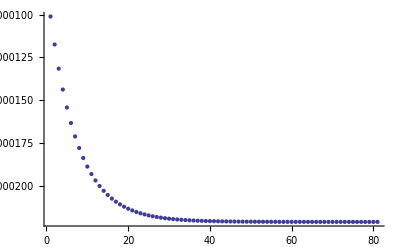

```mathematica
ListPlot[Table[Φ23[5.0,1,ϵs,ϵm,{{1,{0,0,0}}},{0,0,0},NS->i],{i,20,100},DataRange->{20,100}],PlotRange->All]
```

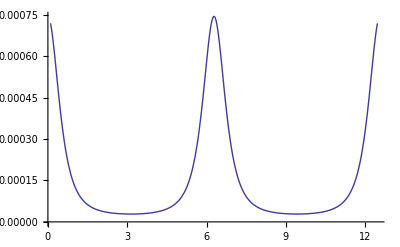

```mathematica
Plot[Φ23[5.0,1,ϵs,ϵm,{{-1,{0,0,-1}},{1,{0,0,1}}},SphericalToCylindrical[{5.0,θ,π}]],{θ,0.1,4π-0.1}]
```

```mathematica
Φmin=Φ23[5.0,1,ϵs,ϵm,{{-1,{0,0,-1}},{1,{0,0,1}}},SphericalToCylindrical[{5.0,π,π}]]
```

0.0000284237

```mathematica
Φmax=Φ23[5.0,1,ϵs,ϵm,{{-1,{0,0,-1}},{1,{0,0,1}}},SphericalToCylindrical[{5.0,2π,π}]]
```

0.000743711

```mathematica
ColorData["TemperatureMap"]
```

ColorDataFunction[{0,1},-Graphics-]

```mathematica
SphericalPlot3D[5,{θ,0.01,π-0.01},{ϕ,0.01,2π-0.01},Mesh->Full,Axes->True,AxesLabel->{"x","y","z"},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["TemperatureMap"][
(Φ23[5.0,1,ϵs,ϵm,{{1,{0,0,0}}},SphericalToCylindrical[{5.0,θ,ϕ}]]-Φmin)/(Φmax-Φmin)
]
]]
```

-Graphics3D-

## Reorganization energy

λ=-1/2∫Δρ[Δϕ(ε_0)-Δϕ(ε_∞)]ⅆV

### Averaging over spherical cavity with radius R

```mathematica
λsphav[R_,d_,δ_,ϵs_,ϵsinf_,ϵm_,ϵminf_,ρi_,ρf_,OptionsPattern[{NS->100}]]:=Module[
{dQtot,nCharges,Sc,dΦtot,dΦinf,dΦav,dρ},
nCharges=Length[ρi];
dρ=Table[{ρf⟦i,1⟧-ρi⟦i,1⟧,ρi⟦i,2⟧},{i,1,nCharges}];
dQtot=Sum[dρ⟦i,1⟧,{i,1,nCharges}];
If[dQtot==0,
Print["Total charge of Δρ is zero!"];0,
Sc=4π R^2 a2bohr^2;
dΦtot=a2bohr^2 R^2 NIntegrate[(Φ1[ϵs,dρ,SphericalToCylindrical[{R,θ,ϕ}]]+Φ23[d,δ,ϵs,ϵm,dρ,SphericalToCylindrical[{R,θ,ϕ}],NS->OptionValue[NS]])Sin[θ],{θ,0,π},{ϕ,-π,π}];
dΦinf=a2bohr^2 R^2 NIntegrate[(Φ1[ϵsinf,dρ,SphericalToCylindrical[{R,θ,ϕ}]]+Φ23[d,δ,ϵsinf,ϵminf,dρ,SphericalToCylindrical[{R,θ,ϕ}],NS->OptionValue[NS]])Sin[θ],{θ,0,π},{ϕ,-π,π}];
dΦav=(dΦtot-dΦinf)/Sc;
(* Print["Average potential on the sphere: ",dΦav," a.u."]; *)
-1/2 dQtot dΦav au2kcal]
];
```

### Averaging over cylindrical cavity with radius R and length L

```mathematica
λcylav[R_,L_,d_,δ_,ϵs_,ϵsinf_,ϵm_,ϵminf_,ρi_,ρf_,OptionsPattern[{NS->100}]]:=Module[{dQtot,nCharges,Sc,dΦtotface1,dΦtotface2,dΦtotfaces,dΦtotside,dΦinfface1,dΦinfface2,dΦinffaces,dΦinfside,dΦtot,dΦinf,dΦav,dρ},
nCharges=Length[ρi];
dρ=Table[{ρf⟦i,1⟧-ρi⟦i,1⟧,ρi⟦i,2⟧},{i,1,nCharges}];
dQtot=Sum[dρ⟦i,1⟧,{i,1,nCharges}];
If[dQtot==0,
Print["Total charge of Δρ is zero!"];0,
Sc=2π R (L+R)a2bohr^2;
dΦtotface1=a2bohr^2 NIntegrate[(Φ1[ϵs,dρ,{ρ,ϕ,-L/2}]+Φ23[d,δ,ϵs,ϵm,dρ,{ρ,ϕ,-L/2},NS->OptionValue[NS]])ρ,{ρ,0,R},{ϕ,-π,π}];
dΦtotface2=a2bohr^2 NIntegrate[(Φ1[ϵs,dρ,{ρ,ϕ,L/2}]+Φ23[d,δ,ϵs,ϵm,dρ,{ρ,ϕ,L/2},NS->OptionValue[NS]])ρ,{ρ,0,R},{ϕ,-π,π}];
dΦtotfaces=dΦtotface1+dΦtotface2;
dΦtotside=a2bohr^2 R NIntegrate[(Φ1[ϵs,dρ,{R,ϕ,z}]+Φ23[d,δ,ϵs,ϵm,dρ,{R,ϕ,z},NS->OptionValue[NS]]),{z,-L/2,L/2},{ϕ,-π,π}];
dΦtot=dΦtotfaces+dΦtotside;

dΦinfface1=a2bohr^2 NIntegrate[(Φ1[ϵsinf,dρ,{ρ,ϕ,-L/2}]+Φ23[d,δ,ϵsinf,ϵminf,dρ,{ρ,ϕ,-L/2},NS->OptionValue[NS]])ρ,{ρ,0,R},{ϕ,-π,π}];
dΦinfface2=a2bohr^2 NIntegrate[(Φ1[ϵsinf,dρ,{ρ,ϕ,L/2}]+Φ23[d,δ,ϵsinf,ϵminf,dρ,{ρ,ϕ,L/2},NS->OptionValue[NS]])ρ,{ρ,0,R},{ϕ,-π,π}];
dΦinffaces=dΦinfface1+dΦinfface2;
dΦinfside=a2bohr^2 R NIntegrate[(Φ1[ϵsinf,dρ,{R,ϕ,z}]+Φ23[d,δ,ϵsinf,ϵminf,dρ,{R,ϕ,z},NS->OptionValue[NS]]),{z,-L/2,L/2},{ϕ,-π,π}];
dΦinf=dΦinffaces+dΦinfside;

dΦav=(dΦtot-dΦinf)/Sc;
(* Print["Average potential on the cylinder surface: ",dΦav," a.u."]; *)
-1/2 dQtot dΦav au2kcal]
];
```

## Single point charge at the center of a spherical cavity:

```mathematica
ρi={{0,{0,0,0}}};
```

```mathematica
ρf={{1,{0,0,0}}};
```

```mathematica
λsphav[5.8,5.8,0.0,ϵs,ϵsinf,ϵm,ϵminf,ρi,ρf,NS->200]
```

7.55065

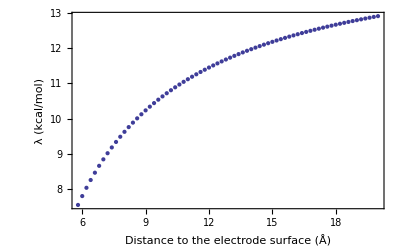

```mathematica
ListPlot[Table[λsphav[5.8,r,0,ϵs,ϵsinf,ϵm,ϵminf,ρi,ρf],{r,5.8,20.0,0.2}],DataRange->{5.8,20.0},Axes->False,Frame->True,FrameLabel->{"Distance to the electrode surface (Å)","λ (kcal/mol)"}]
```

## Single point charge at the center of a cylindrical cavity:

```mathematica
ρi={{0,{0,0,0}}};
```

```mathematica
ρf={{1,{0,0,0}}};
```

```mathematica
λcylav[5.8,11.6,5.8,0.0,ϵs,ϵsinf,ϵm,ϵminf,ρi,ρf,NS->200]
```

5.42444

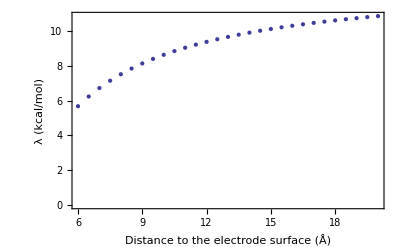

```mathematica
ListPlot[Table[λcylav[5.8,11.6,r,0,ϵs,ϵsinf,ϵm,ϵminf,ρi,ρf],{r,6.0,20.0,0.5}],DataRange->{6,20},Axes->False,Frame->True,FrameLabel->{"Distance to the electrode surface (Å)","λ (kcal/mol)"}]
```

## Point dipole at the center of a spherical cavity:

```mathematica
ρi={{-1,{0,0,-1}},{1,{0,0,1}}};
```

```mathematica
ρf={{1,{0,0,-1}},{-1,{0,0,1}}};
```

```mathematica
λsphav[5.0,5.0,1.0,ϵs,ϵsinf,ϵm,ϵminf,ρi,ρf,NS->50]
```

Total charge of Δρ is zero!

0

## General charge distribution (bcbc Ni complex, 1a-2a pair)

```mathematica
file1a=SystemDialogInput["FileOpen"]
```

/Users/souda/Documents/Projects/SAM-electrostatics/bcbc-nbo-1a.csv

```mathematica
data1a=ReadList[file1a,{Number,Word,Real,{Real,Real,Real}}];
```

```mathematica
ρ1a=data1a⟦All,{3,4}⟧;
```

```mathematica
file2a=SystemDialogInput["FileOpen"]
```

/Users/souda/Documents/Projects/SAM-electrostatics/bcbc-nbo-2a-charges.csv

```mathematica
data2a=ReadList[file2a,{Number,Word,Real}];
```

```mathematica
ρ1a⟦1⟧
```

{1.43857,{-0.02056,0.244065,-0.259379}}

```mathematica
data2a⟦5,3⟧
```

-0.150804

```mathematica
ρ2a=ReplacePart[ρi,{i_,1}->data2a⟦i,3⟧];
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

### Spherical cavity

```mathematica
Graphics3D[{
{Point[ρ1a⟦All,2⟧]},
{Sphere[ρ1a⟦All,2⟧,1.5]},
{Opacity[0.5],Sphere[{0,0,0},7.5]},{Arrowheads[0.02],Arrow[{{-10,0,0},{10,0,0}}]},
{Arrowheads[0.02],Arrow[{{0,-10,0},{0,10,0}}]},
{Arrowheads[0.02],Arrow[{{0,0,-10},{0,0,10}}]},
{Text[Style["x",Italic,14],{10.5,0,0}]},
{Text[Style["y",Italic,14],{0,10.5,0}]},
{Text[Style["z",Italic,14],{0,0,10.5}]}
},Boxed->False]
```

-Graphics3D-

Reorganization energy (kcal/mol):

```mathematica
λsphav[7.5,7.5,0,ϵs,ϵsinf,ϵm,ϵminf,ρ1a,ρ2a,NS->100]
```

5.91303

Dependence on the distance to the electrode surface:

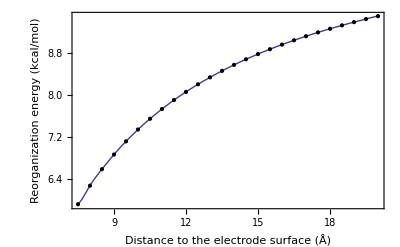

```mathematica
ListLinePlot[Table[λsphav[7.5,d,0,ϵs,ϵsinf,ϵm,ϵminf,ρ1a,ρ2a,NS->100],{d,7.5,20.0,0.5}],DataRange->{7.5,20},Axes->False,Frame->True,FrameLabel->{"Distance to the electrode surface (Å)","λ (kcal/mol)"},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},InterpolationOrder->3,Mesh->Full,MeshStyle->PointSize[Medium],PlotLabel->"Spherical cavity"]
```

### Cylindrical cavity

```mathematica
Graphics3D[{
{Point[ρ1a⟦All,2⟧]},
{Sphere[ρ1a⟦All,2⟧,1.5]},
{Opacity[0.5],Cylinder[{{0,0,-5.5},{0,0,5.5}},7.0]},{Arrowheads[0.02],Arrow[{{-10,0,0},{10,0,0}}]},
{Arrowheads[0.02],Arrow[{{0,-10,0},{0,10,0}}]},
{Arrowheads[0.02],Arrow[{{0,0,-10},{0,0,10}}]},
{Text[Style["x",Italic,14],{10.5,0,0}]},
{Text[Style["y",Italic,14],{0,10.5,0}]},
{Text[Style["z",Italic,14],{0,0,10.5}]}
},Boxed->False]
```

-Graphics3D-

Reorganization energy (kcal/mol):

```mathematica
λcylav[7.0,11.0,7.0,0,ϵs,ϵsinf,ϵm,ϵminf,ρ1a,ρ2a,NS->100]
```

5.70176

Dependence on the distance to the electrode surface:

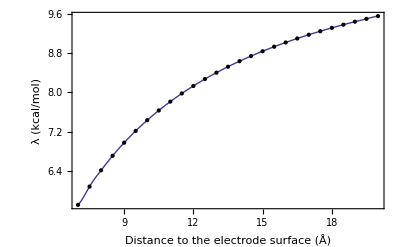

```mathematica
ListLinePlot[Table[λcylav[7.0,11.0,d,0,ϵs,ϵsinf,ϵm,ϵminf,ρ1a,ρ2a,NS->100],{d,7.0,20.0,0.5}],DataRange->{7.0,20.0},Axes->False,Frame->True,FrameLabel->{"Distance to the electrode surface (Å)","λ (kcal/mol)"},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},InterpolationOrder->3,Mesh->Full,MeshStyle->PointSize[Medium],PlotLabel->"Cylindrical cavity"]
```